# Systematic Randomness Testing

Emmy/Noah Blumenthal

Jonathan Gorard

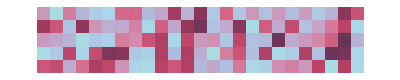

```mathematica
ArrayPlot[Partition[RandomReal[{0,1},125],25],]
```

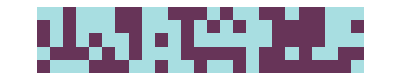

```mathematica
ArrayPlot[Partition[Take[rule30seq,125],25],]
```

## Introduction

This project aims to implement systematic randomness testing into the Wolfram Language through both theoretically–designed tests and Monte Carlo–designed tests. The tests use a sequence of either zeros and ones or reals between zero and one as input. The tests return a p–value evaluating the null hypothesis that the sequence is indeed random. The general design of the tests is to first create a test statistic based on some property of random sequences. A sampling distribution is then derived either theoretically or using a Monte Carlo method in order to generate the p–values. 

The project implements equidistribution and diehard tests in order to evaluate the randomness of a sequence. The general applications of a the project include evaluating random number generation techniques like linear feedback shift registers or cellular automata rules or evaluating the quality of a statistical sampling technique.

The following is a list of tests that are developed by method and type:

```mathematica
Grid[{{"","Monte Carlo method","Theoretical method"},{"0s and 1s","Serial","Chi square
Spectral
Runs
CUSUM
Arcsine law
Kolmogorov–Smirnov"},{"Reals between 0 and 1","Runs (length)
Runs (counts)","Chi square
Spectral
Kolmogorov–Smirnov"}},Dividers->All]//Text
```

| Monte Carlo method | Theoretical method
0s and 1s | Serial | Chi square
Spectral
Runs
CUSUM
Arcsine law
Kolmogorov–Smirnov
Reals between 0 and 1 | Runs (length)
Runs (counts) | Chi square
Spectral
Kolmogorov–Smirnov

List of resource functions:

"[◼]" | "ArcsineLawRandomnessTest"

"[◼]" | "BinaryRunRandomnessTest"

"[◼]" | "ChiSquareRandomnessTest"

"[◼]" | "CUSUMMaxRandomnessTest"

"[◼]" | "RunCountRandomnessTest"

"[◼]" | "RunLengthRandomnessTest"

"[◼]" | "SerialRandomnessTest"

"[◼]" | "SpectralRandomnessTest"

## Implementing

## Chi square equidistribution test

The first test we will examine is a relatively simple, ubiquitous test: the chi square test for independence. In this approach we will use the chi square test to measure how the observed values differ from expected values.

#### Zeros and ones

The expected value distribution of zeros and ones is very simple. There is a 1/2 probability that a variate will be 0 and a 1/2 probability that a variate will be 1. Therefore, we can set up a statistic like the following:

```mathematica
chiSquareTestStatIntegers[seq_]:=(Total[seq]-1/2 Length[seq])^2/(1/2 Length[seq])(*observed number of ones*)+((Length[seq]-Total[seq])-1/2 Length[seq])^2/(1/2 Length[seq])(*observed number of zeros*);
```

We know that this statistic will follow a chi square distribution with ν = 1. Let’s confirm:

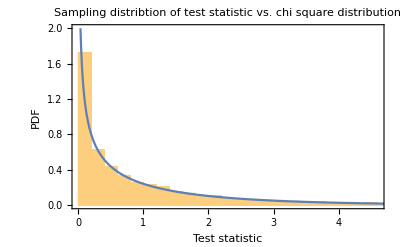

```mathematica
Show[Histogram[Table[chiSquareTestStatIntegers[RandomInteger[{0,1},10000]],100000],Automatic,"PDF"],Plot[PDF[ChiSquareDistribution[1],x],{x,0,10},PlotRange->{0,2}],]
```

Therefore, we can construct a p-value as follows:

```mathematica
chiSquareTestPValueIntegers[seq_]:=1.-CDF[ChiSquareDistribution[1],chiSquareTestStatIntegers[seq]]
```

To check our work, we can construct a probability plot comparing the distribution of p-values to the uniform distribution.

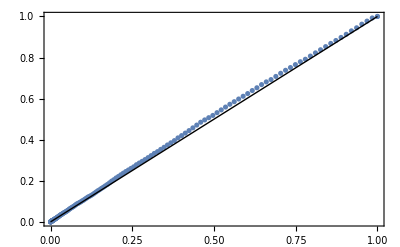

```mathematica
ProbabilityPlot[Table[chiSquareTestPValueIntegers[RandomInteger[{0,1},10000]],10000],UniformDistribution[]]
```

We observe that the rate of type-I error behaves as expected for a well-functioning test. This, of course, assumes that the pseudo–random number generator that is RandomInteger is truly “random”—whatever that may mean.

#### Random reals between zero and one

Again, with the chi square test for independence, we must compare observed values to expected values. For continuous distributions, we must choose bins in which we have expected values. For our purposes, we will choose bins of size 1/n where n is the length of the sequence. Using this bin specification, we know that the expected number of numbers we should observe in each bin should be 1. With this information, we can create a test statistic:

```mathematica
chiSquareTestStatReals[seq_]:=Total[(BinCounts[seq,1/Length[seq]]-1)^2/1](*note we use the listable atribute of squaring and basic arithmetic*)
```

This distribution should follow the chi square distribution with ν = n -2 where n is the length of the sequence. Let’s confirm:

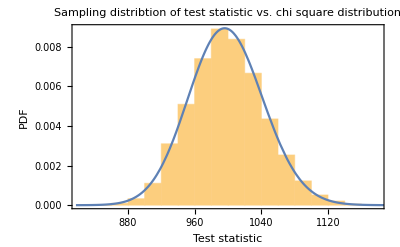

```mathematica
Show[Histogram[Table[chiSquareTestStatReals[RandomReal[{0,1},1000]],10000],Automatic,"PDF"],Plot[PDF[ChiSquareDistribution[998],x],{x,0,1500},],]
```

We can then construct a p-value:

```mathematica
chiSquareTestPValueReals[seq_]:=1.-CDF[ChiSquareDistribution[Length[seq]-2],chiSquareTestStatReals[seq]];
```

Again, to check our work, we can construct a probability plot comparing the distribution of p-values to the uniform distribution.

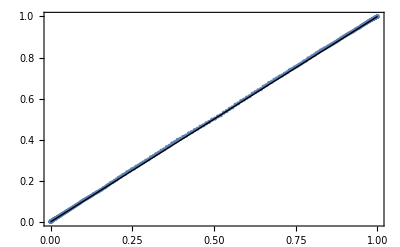

```mathematica
ProbabilityPlot[Table[chiSquareTestPValueReals[RandomReal[{0,1},1000]],10000],UniformDistribution[]]
```

Again, it seems as if we are successful!

## The Kolmogorov–Smirnov distribution fit test

The Kolmogorov–Smirnov test is a power distribution fit test that compares an empirical CDF to a known CDF. The Kolmogorov–Smirnov test is relatively simple to formulate, but fortunately, it is already implemented in the Wolfram Language. We can then apply it to test for equidistribution of a sequence:

```mathematica
sequence=RandomReal[{0,1},10000];
```

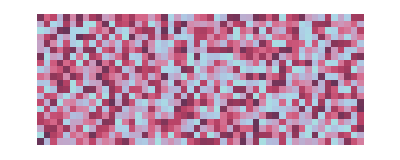

```mathematica
ArrayPlot[Partition[Take[sequence,1000],50],ImageSize->Full,ColorFunction->"CandyColors"]
```

```mathematica
KolmogorovSmirnovTest[sequence,UniformDistribution[]]
```

0.383461

It is important to note that the Kolmogorov–Smirnov test does not handle ties very well:

```mathematica
duplicateSequence=Flatten[{sequence,sequence}];
```

```mathematica
KolmogorovSmirnovTest[duplicateSequence,UniformDistribution[]]
```

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.0745876

#### A remark on equidistribution tests

Equidistribution tests are very easily fooled! They do not care about order, permutations, runs, spectra, or anything like these complex properties. Here’s an example of how equidistribution tests is completely fooled:

```mathematica
nonrandomSequence=Range[0,1,.0001];
```

```mathematica
KolmogorovSmirnovTest[nonrandomSequence,UniformDistribution[]]
```

1.

```mathematica
chiSquareTestPValueReals[nonrandomSequence]
```

General::munfl: Exp[-37587.9] is too small to represent as a normalized machine number; precision may be lost.

1.

## Serial test

The serial test examines the frequency of the following pairs within the overall sequence:

```mathematica
Row[Tuples[{0,1},2],"     "]
```

{0,0}{0,1}{1,0}{1,1}

For example, the sequence

```mathematica
sequence=RandomInteger[{0,1},100];
sequence//Row
```

1101011001101110111100101100100110011000110110000011101111100000110011001100000111100101000111101010

has the associated counts

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{16,23,24,21}

where the order is that of the pairs list above.

We can create a chi square–like statistic that measures the deviation from expected frequency

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))

where n is the sequence length and μ_freq is the expected frequency with which the the pair occurs. These frequencies are computed empirically:

```mathematica
mcts[n_,samplesize_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],samplesize]];
```

This function counts the mean number of pairs of a particular type observed within a large number, samplesize, of random sequences.

We can observe how these expected frequencies vary with sequence length:

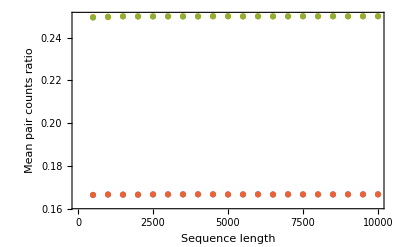

```mathematica
{pts00,pts01,pts10,pts11}=ParallelTable[{{n,n,n,n},mcts[n,10000]/n}ᵀ,{n,500,10000,500}]ᵀ;
ListPlot[{pts00,pts01,pts10,pts11},Frame->True,FrameLabel->{"Sequence length","Mean pair counts ratio"}]
```

This figure displays how the expected frequencies are invariant under sequence length variation.

After discovering this, we can come up with one set of constants that will work for any sequence length:

```mathematica
$mctsrat=mcts[1000,100000]/1000
```

{0.166564,0.249761,0.249774,0.166603}

And with this in mind we can finally construct a test statistic:

```mathematica
SerialTestStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)];
```

As we chose a chi square–like statistic, we can anticipate that the test statistic will follow a gamma distribution.

```mathematica
serialsamplingdist[n_,samplesize_]:=ParallelTable[SerialTestStat[RandomInteger[{0,1},n]],samplesize]
```

```mathematica
serialdistsample1000=serialsamplingdist[1000,100000];
```

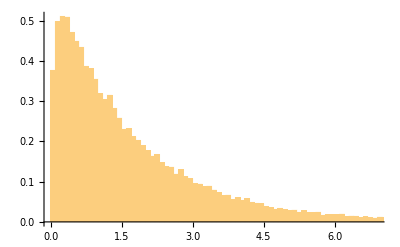

```mathematica
Histogram[serialdistsample1000,{.1},"PDF"]
```

```mathematica
serialfitdist1000=FindDistribution[serialdistsample1000,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[1.12212,1.53172]

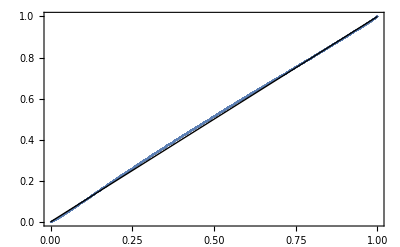

```mathematica
ProbabilityPlot[serialdistsample1000,serialfitdist1000]
```

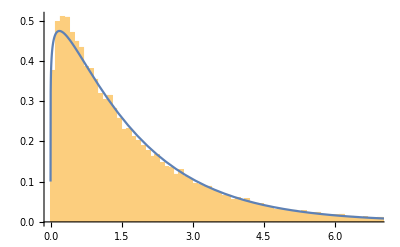

```mathematica
Show[Histogram[serialdistsample1000,{.1},"PDF"],Plot[PDF[serialfitdist1000,x],{x,0,10}]]
```

We can see that this distribution fits relatively well. Let’s now investigate how the distribution parameters α and β vary with sequence length.

```mathematica
αβparams[n_,samplesize_]:=FindDistributionParameters[serialsamplingdist[n,samplesize],GammaDistribution[α,β]]
```

```mathematica
paramvslength=Table[{{n,n},{α,β}}ᵀ/.αβparams[n,10000],{n,100,10000,1000}];
```

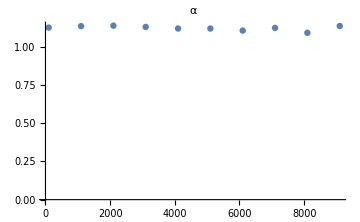
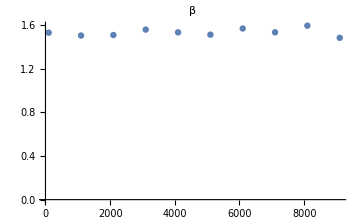

```mathematica
Row@{ListPlot[paramvslengthᵀ⟦1⟧,],ListPlot[paramvslengthᵀ⟦2⟧,]}
```

We can see that the parameters hardly vary and do not vary consistently with list length. We can then find parameters we like.

```mathematica
$serialparams=αβparams[10000,10000]
```

{α→1.10793,β→1.53947}

```mathematica
$serialfitdist=GammaDistribution[α,β]/.$serialparams
```

GammaDistribution[1.10793,1.53947]

Our p–value is then of the form:

```mathematica
1-CDF[$serialfitdist,SerialTestStat[RandomInteger[{0,1},10000]]]
```

0.522471

As a final test, we want to confirm that the distribution of p–values follows a uniform distribution:

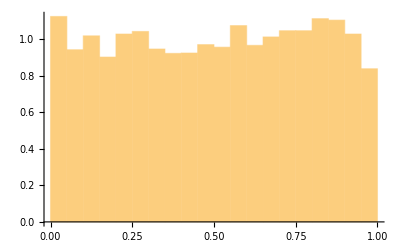

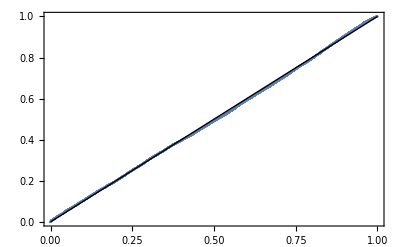

```mathematica
1-CDF[$serialfitdist,SerialTestStat[#]]&/@RandomInteger[{0,1},{10000,10000}];
Histogram[%,Automatic,"PDF"]
ProbabilityPlot[%%,UniformDistribution[]]
```

We can see that the p–values are uniformly distributed from our Monte Carlo method.

#### Discussion

This method is powerful as it examines the frequency and ordering of pairs. However, this method is contingent on one large assumption—that the Wolfram Language pseudorandom number generator is truly pseudorandom. Or rather, that it is pseudorandom enough. A Monte Carlo approach is often very powerful for these sorts of statistics; however, it is important to be weary of such assumptions.

## Runs tests

In these tests, we will investigate runs of both 0s and 1s and random reals between 0 and 1. A run is a sequence that fits a particular pattern until it is reset. For random reals, we will use increasing runs. For example, in the sequence

```mathematica
sequence=RandomReal[{0,1},100];
Row[sequence,", "]
```

, , 0.3400750.5758180.7157820.029690.2823670.04113640.9141810.5912050.9763390.9543410.5685020.08568070.08437660.9915130.6109590.9133420.906590.2372970.8534350.3259230.4100940.03717690.825150.6781170.09094580.5352990.8101320.2337550.6667260.6120640.6134040.1226470.654480.3618070.6596540.8038710.5294130.6356610.4200310.4125320.7630120.3134450.1173780.2030440.7778110.5515950.4347710.7096410.1533850.4925830.5463110.343170.04422490.3996610.3471830.8920160.8321590.1100920.1258730.08883590.7755110.3700720.04787510.2377650.535620.939380.2457540.08993780.5359480.1902380.7052990.10820.9303250.1604550.7852520.138620.5454050.01987180.07722260.7515770.483660.4756980.6531010.3152410.7583580.9282310.5649570.1154680.8761110.555560.01812620.5083760.931630.6193880.1867940.3236650.5713260.01430930.3910640.298401

The associated runs are

```mathematica
Row[Split[sequence,#1<#2&],", "]
```

, , {0.340075,0.575818,0.715782}{0.02969,0.282367}{0.0411364,0.914181}{0.591205,0.976339}{0.954341}{0.568502}{0.0856807}{0.0843766,0.991513}{0.610959,0.913342}{0.90659}{0.237297,0.853435}{0.325923,0.410094}{0.0371769,0.82515}{0.678117}{0.0909458,0.535299,0.810132}{0.233755,0.666726}{0.612064,0.613404}{0.122647,0.65448}{0.361807,0.659654,0.803871}{0.529413,0.635661}{0.420031}{0.412532,0.763012}{0.313445}{0.117378,0.203044,0.777811}{0.551595}{0.434771,0.709641}{0.153385,0.492583,0.546311}{0.34317}{0.0442249,0.399661}{0.347183,0.892016}{0.832159}{0.110092,0.125873}{0.0888359,0.775511}{0.370072}{0.0478751,0.237765,0.53562,0.93938}{0.245754}{0.0899378,0.535948}{0.190238,0.705299}{0.1082,0.930325}{0.160455,0.785252}{0.13862,0.545405}{0.0198718,0.0772226,0.751577}{0.48366}{0.475698,0.653101}{0.315241,0.758358,0.928231}{0.564957}{0.115468,0.876111}{0.55556}{0.0181262,0.508376,0.93163}{0.619388}{0.186794,0.323665,0.571326}{0.0143093,0.391064}{0.298401}

For another sequence of 0s and 1s, we obtain the runs by simply splitting the list:

```mathematica
sequence=RandomInteger[{0,1},100];
Row[sequence]
```

1001110000001001100101011100110100100111101010000100011010010111001001101110011111001010000001011000

```mathematica
Row[Split[sequence],", "]
```

, , {1}{0,0}{1,1,1}{0,0,0,0,0,0}{1}{0,0}{1,1}{0,0}{1}{0}{1}{0}{1,1,1}{0,0}{1,1}{0}{1}{0,0}{1}{0,0}{1,1,1,1}{0}{1}{0}{1}{0,0,0,0}{1}{0,0,0}{1,1}{0}{1}{0,0}{1}{0}{1,1,1}{0,0}{1}{0,0}{1,1}{0}{1,1,1}{0,0}{1,1,1,1,1}{0,0}{1}{0}{1}{0,0,0,0,0,0}{1}{0}{1,1}{0,0,0}

Now that we have a definition of runs, we can begin creating statistics using them.

### How long are runs in a sequence?

The first statistic we will construct will measure the length of runs. Our approach will again utilize a Monte Carlo method. To measure runs:

```mathematica
runsup[seq_]:=Split[seq,#1<#2&];
```

In order to count lengths of runs:

```mathematica
runLengthDist[seq_]:=Length/@runsup[seq]
```

The distribution of run lengths within a random sequence:

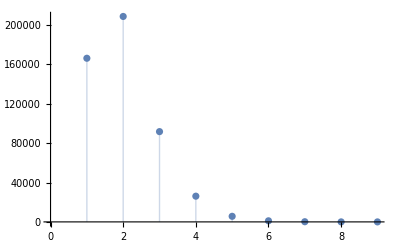

```mathematica
ListPlot[Counts@runLengthDist@RandomReal[{0,1},1000000],Filling->Axis]
```

We then want to investigate if these ratios vary with sequence length:

```mathematica
sequence=RandomReal[{0,1},10000];
Manipulate[Histogram[runLengthDist[Take[sequence,n]],{1},"PDF",PlotRange->{{0,10},{0,1}},PlotLabel->"n = "<>ToString[n]],{n,1,10000,1}]
```

We can see that the run lengths quickly converge to a constant distribution. With this we can then calculate a constant–the mean run length:

```mathematica
$meanRunLength=Mean[ParallelMap[ N@Mean[runLengthDist[#]]&,RandomReal[{0,1},{10000,5000}]]]
```

2.00004

We will then construct another chi–square like test statistic:

```mathematica
RunLengthStat[seq_]:=Total[(runLengthDist[seq]-$meanRunLength)^2/($meanRunLength)];
```

We then need to assess the distribution of this test statistic:

```mathematica
Manipulate[Histogram[RunLengthStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

We can see that this distribution fits the normal distribution relatively well:

```mathematica
Manipulate[ProbabilityPlot[RunLengthStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

Next, we will demonstrate that the mean follows a linear trend and is proportional to the sequence length

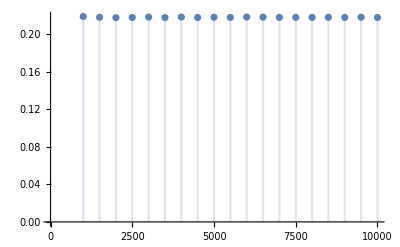

```mathematica
DiscretePlot[Mean[RunLengthStat[#]&/@RandomReal[{0,1},{1000,seqleng}]]/seqleng,{seqleng,1000,10000,500}]
```

We can then construct a function that will return the approximate sample mean:

```mathematica
runlengthμ[seqleng_]=seqleng Mean[RunLengthStat[#]&/@RandomReal[{0,1},{10000,10000}]]/10000
```

We then proceed with a similar procedure regarding standard deviation—the other parameter for our distribution:

```mathematica
DiscretePlot[StandardDeviation[RunLengthStat[#]&/@RandomReal[{0,1},{10000,seqleng}]]/seqleng,{seqleng,1000,10000,500}]
```

$Aborted

We see that this is not quite a linear pattern. We can hypothesize using a non–linear model:

```mathematica
standarddevratvsseqleng=ParallelTable[{seqleng,StandardDeviation[RunLengthStat[#]&/@RandomReal[{0,1},{1000,seqleng}]]/seqleng},{seqleng,1000,10000,500}];
```

```mathematica
nlm=NonlinearModelFit[standarddevratvsseqleng,a x^b,{a,b},x]
```

FittedModel[0.47521/x^0.500196]

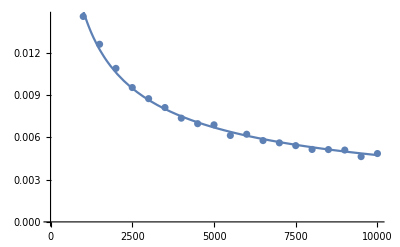

```mathematica
Show[ListPlot[standarddevratvsseqleng],Plot[nlm[seqleng],{seqleng,0,10000}]]
```

We see that this fits very well. We then have

σ/seqleng≈nlm[seqleng]
σ≈sqeleng nlm[seqleng]

```mathematica
runlengthσ[seqleng_]=seqleng nlm[seqleng]
```

All together:

stat \[Distributed] NormalDistribution[statdistμ[seqleng],statdistσ[seqleng]]

Finally, we can calculate a two–tailed p–value given a sequence:

```mathematica
2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runlengthμ[Length[sequence]],runlengthσ[Length[sequence]]],RunLengthStat[sequence]]
```

0.601173

Like before, we will evaluate the rate of type I error by comparing the distribution of p–values to the uniform distribution:

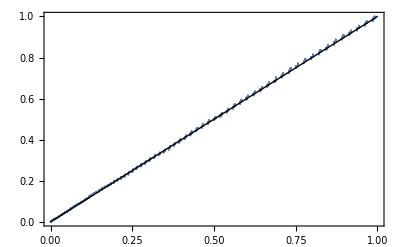

```mathematica
ProbabilityPlot[Table[2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runlengthμ[5000],runlengthσ[5000]],RunLengthStat[RandomReal[{0,1},5000]]],10000],UniformDistribution[]]
```

### How many runs do we expect a sequence to have?

The next statistic we create will count the total amount of runs a sequence has. The statistic is then:

```mathematica
RunCountStat=Length[Split[#,(#1<#2&)]]&;
```

This distribution follows a normal distribution:

```mathematica
Manipulate[Histogram[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

```mathematica
Manipulate[ProbabilityPlot[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]],{seqleng,5000}]
```

Again, we will investigate how the mean varies over sequence length:

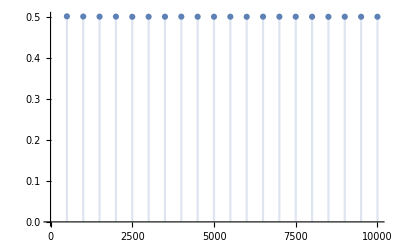

```mathematica
DiscretePlot[Mean[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]]/seqleng,{seqleng,500,10000,500}]
```

The mean to sequence length ratio is constant, making the mean given a sequence length. This is unsurprising because as we observed before, the mean sequence length is two. Therefore, the mean number of runs should be half the sequence length.

```mathematica
runcountμ[seqleng_]=seqleng/2
```

seqleng/2

Standard deviation is a bit more complicated:

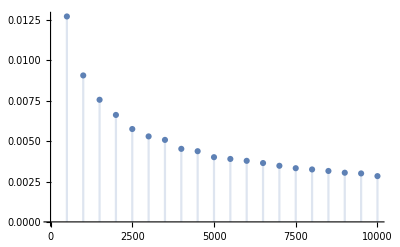

```mathematica
DiscretePlot[StandardDeviation[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]]/seqleng,{seqleng,500,10000,500}]
```

Again, we get a non–linear pattern. Let’s fit a non–linear model:

FittedModel[0.291155/x^0.50107]

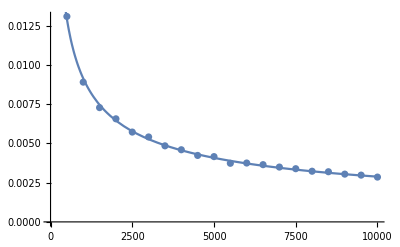

```mathematica
runcountstdevvsseqleng=ParallelTable[{seqleng,StandardDeviation[RunCountStat/@RandomReal[{0,1},{1000,seqleng}]]/seqleng},{seqleng,500,10000,500}];
nlm=NonlinearModelFit[runcountstdevvsseqleng,a x^b,{a,b},x]
Show[ListPlot[runcountstdevvsseqleng],Plot[nlm[x],{x,0,10000},PlotRange->All]]
```

The standard deviation given a sequence length is then:

```mathematica
runcountσ[seqleng_]=nlm[seqleng] seqleng
```

0.303833 seqleng^0.493785

We then have our distribution:

```mathematica
$runcountdist[seqleng_]=NormalDistribution[runcountμ[seqleng],runcountσ[seqleng]]
```

NormalDistribution[seqleng/2,0.303833 seqleng^0.493785]

We can finally compose a two–tailed p–value:

```mathematica
2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runcountμ[Length[sequence]],runcountσ[Length[sequence]]],RunCountStat[sequence]]
```

0.530441

And we will assess the rate of type I error:

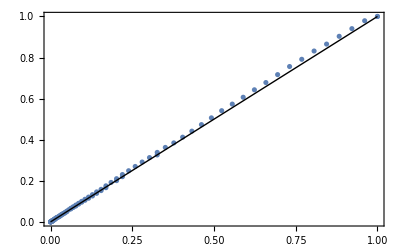

```mathematica
ProbabilityPlot[Table[2Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[runcountμ[5000],runcountσ[5000]],RunCountStat[RandomReal[{0,1},5000]]],10000],UniformDistribution[]]
```

### How many runs does a sequence of zeros and ones have?

This test is taken entirely from the NIST publication. It only assesses sequences of 0s and 1s. Additionally, it is theoretically derived. The test statistic the publication gives is

```mathematica
NISTRunsstat=Length@Split@#&;
```

And the publication assigns the associated p–value.

```mathematica
NISTRunspval=Erfc[Abs[Length@Split@#1-2 Length[#1] #2 (1-#2)]/(2. √(2Length[#1]) #2 (1-#2))]&[#,Total[#]/Length[#]]&;
```

We can demonstrate this test on a sequence:

```mathematica
sequence=RandomInteger[{0,1},10000];
NISTRunspval[sequence]
```

0.357017

Finally, we can assess this test by assessing the rate of type I error:

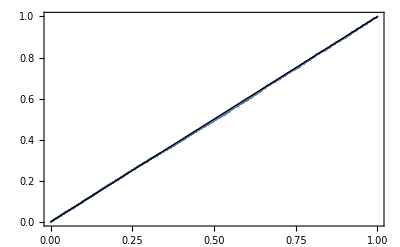

```mathematica
ProbabilityPlot[NISTRunspval/@RandomInteger[{0,1},{10000,10000}],UniformDistribution[]]
```

## Differences tests

The next test we will examine tests the distribution of differences between successive sequence bits. We will simply use the Kolmogorov–Smirnov test the difference between the observed distribution and the expect distribution. The expected distribution is TriangularDistribution[{-1,1}]:

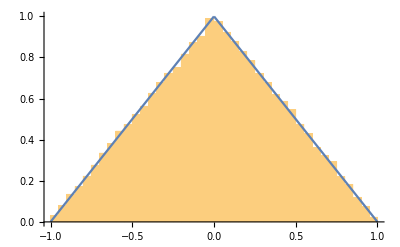

```mathematica
Show[Histogram[Differences[RandomReal[{0,1},100000]],50,"PDF"],Plot[PDF[TriangularDistribution[{-1,1}],x],{x,-1,1}]]
```

Our test is then simple. The p–value is:

```mathematica
sequence=RandomReal[{0,1},100000];
KolmogorovSmirnovTest[Differences[sequence],TriangularDistribution[{-1,1}]]
```

0.968664

We can test the type 1 error:

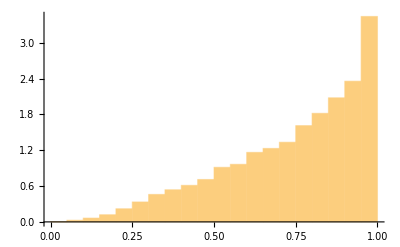

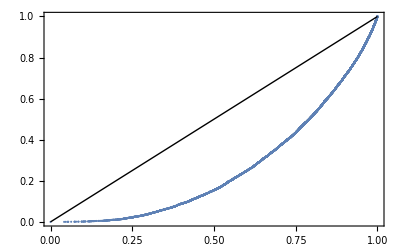

```mathematica
KolmogorovSmirnovTest[Differences[#],TriangularDistribution[{-1,1}]]&/@RandomReal[{0,1},{10000,10000}];
Histogram[%,Automatic,"PDF"]
ProbabilityPlot[%%,UniformDistribution[]]
```

We immediately see that the rate of type I error is not consistent with the idea that a valid test should have uniformly distributed p–values. This indicates that the test is not valid. It is not clear why this test failed. It is possible, but unlikely, that this result is demonstrating that the pseudorandom number generator that the Wolfram Language is using is not valid.

## Spectral tests

The spectral test will use the discrete cosine transform to assess the randomness of data. The transformed data should be homogeneous over frequency space and, overall, should be normally distributed. The transformed data should be normally distributed because the transformed data is obtained by:

(∑_(r=1)^n Cos[(π (-1/2+r) (-1+s))/n] u[r])/(√n)

where u[r] is the rth random number in the sequence, s is the frequency parameter, and n is the length of the sequence. This can be re–expressed in the form:

FourierDCT[U][s]=U/(√n)·a[s]

where U is the sequence, a[s] is a list of constants, and · is the dot product. This form tells us that each individual point is a sum of random variables. If these variables are truly independently and identically distributed, they should follow the normal distribution:

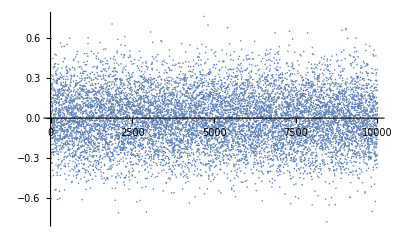

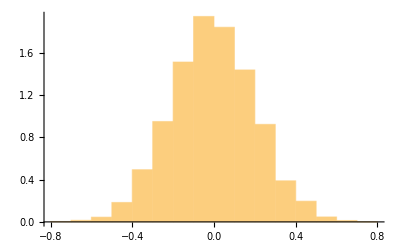

```mathematica
sequence=RandomReal[{0,1},10000];
ListPlot[Rest@FourierDCT@sequence,PlotRange->All]
Histogram[Rest@FourierDCT@sequence,Automatic,"PDF"]
```

Our task then is to simply perform a Kolmogorov–Smirnov test for normality on the transformed data:

```mathematica
KolmogorovSmirnovTest[Rest@FourierDCT@sequence,Automatic,"PValue"]
```

0.757535

## Sequential sums tests

This test is entirely developed by the NIST publication.

The test statistic for this test is based on the idea of generating a random walk from a list of zeros and ones. First, we transform the sequence and then accumulate the values.

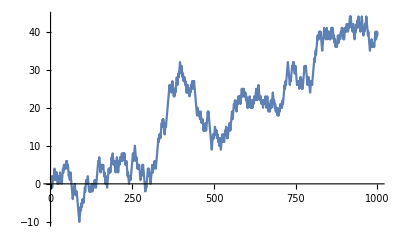

```mathematica
sequence=RandomInteger[{0,1},1000];
ListLinePlot[Accumulate[2 sequence-1]]
```

We can visualize the distribution of these random walks:

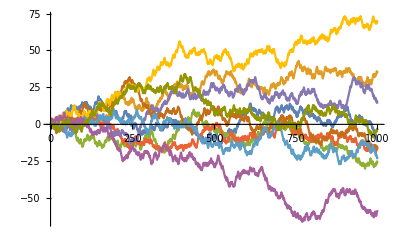

```mathematica
ListLinePlot[Accumulate[2 #-1]&/@RandomInteger[{0,1},{10,1000}]]
```

For the statistic, we will look at the maximum distance away from zero that the walk obtains:

```mathematica
CUSUMmaxstat[seq_]:=Max@Abs@Accumulate[2 seq-1];
```

The stationary distribution is approximately normal. The publication uses this property to derive the following formula for the p–value:

```mathematica
Φ[x_]=CDF[NormalDistribution[],x];
CUSUMmaxpval=Function[{z,n},1.-Sum[Φ[(z(4k+1))/(√n)]-Φ[(z(4k-1))/(√n)],{k,Floor[(-n/z+1)/4],(n/z-1)/4,1}]+Sum[Φ[(z(4k+3))/(√n)]-Φ[(z(4k+1))/(√n)],{k,Floor[(-n/z-3)/4],(n/z-1)/4,1}]][CUSUMmaxstat[#],Length[#]]&;
```

We can test the rate of type I error:

General::munfl: -0.5 2.98655×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

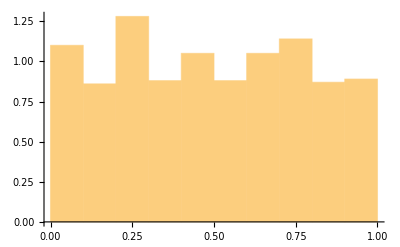

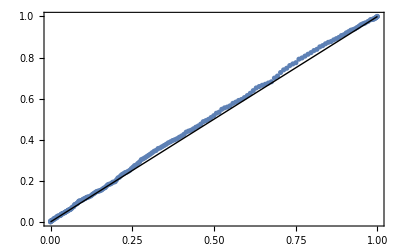

```mathematica
CUSUMmaxpval/@RandomInteger[{0,1},{1000,10000}];
Histogram[%,Automatic,"PDF"]
ProbabilityPlot[%%,UniformDistribution[]]
```

## Arcsine test

This test utilizes the arcsine law as described in Lorek, Los, Gotfryd, and Zagórski's publication. The arcsine law states that given a variable X—the percentage of a random walk generated by a sequence of random reals spends above (or equivalently below) 0—X will be distributed according to a particular ‘arcsine distribution’:

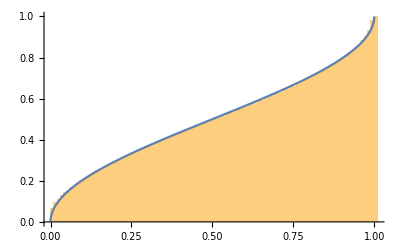

```mathematica
Table[(Length@Cases[Accumulate[2#-1]&@RandomReal[{0,1},1000],x_/;x>0])/1000,10000];
Show[Histogram[%,100,"CDF"],Plot[2/π ArcSin[√x],{x,0,1}]]
```

The formula for the CDF of the distribution is

```mathematica
CDF[x]=((2 arcsin(√x))/π).
```

Our statistic is then the percentage of time a random walk generated from our sequence spends above 0:

```mathematica
Arcsinelawstat[seq_]:=(Length@Cases[Accumulate[2#-1]&@seq,x_/;x>0])/Length[seq];
```

And we create a two–tailed p–value:

```mathematica
Arcsinelawpval[stat_]:=2 Min@{1-#,#}&[2/π ArcSin[√stat]];
```

We can confirm the validity of this test by examining the distribution of p–values to test the type I error:

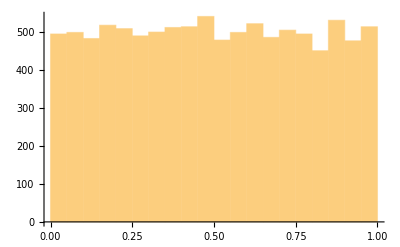

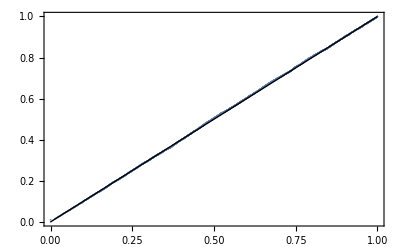

```mathematica
N@Arcsinelawpval[Arcsinelawstat[#]]&/@RandomReal[{0,1},{10000,10000}];
Histogram[%]
ProbabilityPlot[%%,UniformDistribution[]]
```

## Variates of arbitrary distributions

We can extend the scope of tests on sequences of random reals between 0 and 1. Using the property that the CDF of a distribution applied to its variates yield a uniform distribution, we can test the randomness of a sequence of variates from a known distribution. An example using the run length test:

```mathematica
variates=RandomVariate[NormalDistribution[],10000];
```

```mathematica
transformedvariates=CDF[NormalDistribution[],variates];
```

```mathematica
{{"[◼]", "RunLengthRandomnessTest"}}[transformedvariates,"TestStatistic"]
```

2190.21

```mathematica
{{"[◼]", "RunLengthRandomnessTest"}}[transformedvariates,"PValue"]
```

0.849354

## Applications

## Rule 30

[Introduce rule 30]

At the α = .01 significance level, the center column of rule 30 passes all tests designed to test the randomness of sequences of 0s and 1s:

```mathematica
rule30seq=CellularAutomaton[30, {{1}, 0}, {10000,0}]ᵀ⟦1⟧;
```

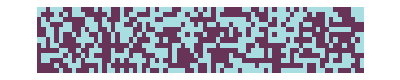

```mathematica
ArrayPlot[Partition[Take[rule30seq,8*125],3*25],]
```

```mathematica
{{"[◼]", "ChiSquareRandomnessTest"}}[rule30seq]
```

0.515713

```mathematica
N@{{"[◼]", "ArcsineLawRandomnessTest"}}[rule30seq]
```

0.332579

```mathematica
{{"[◼]", "BinaryRunRandomnessTest"}}[rule30seq]
```

0.759777

```mathematica
{{"[◼]", "CUSUMMaxRandomnessTest"}}[rule30seq]
```

0.370412

```mathematica
{{"[◼]", "SerialRandomnessTest"}}[rule30seq]
```

0.711583

```mathematica
{{"[◼]", "SpectralRandomnessTest"}}[rule30seq]
```

0.226717

## Shift Register Sequences

We can also apply these tests to assess the randomness of shift register sequences. Shift registers are entities that generate sequences given certain internal characteristics. Shift registers are similar to cellular automata as they use feedback from previous sequence bits to create the next bit and. Shift registers can also be described using a characteristic polynomial. For this example, we will examine a maximal–length linear shift register sequence:

```mathematica
shiftregistersequence=ShiftRegisterSequence[12];
```

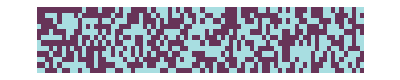

```mathematica
ArrayPlot[Partition[Take[shiftregistersequence,1000],80],]
```

The shift register sequence passes several tests very well:

```mathematica
{{"[◼]", "ChiSquareRandomnessTest"}}[shiftregistersequence]
```

0.987532

```mathematica
N@{{"[◼]", "ArcsineLawRandomnessTest"}}[shiftregistersequence]
```

0.291655

```mathematica
{{"[◼]", "BinaryRunRandomnessTest"}}[shiftregistersequence]
```

0.987529

```mathematica
{{"[◼]", "CUSUMMaxRandomnessTest"}}[shiftregistersequence]
```

0.567182

```mathematica
{{"[◼]", "SerialRandomnessTest"}}[shiftregistersequence]
```

0.997039

It is important to note that the sequence does seem to perform artificially highly on several tests. This observation is not cause to reject a hypothesis of randomness, but it is somewhat suspicious as it suggests that patterns within the generated sequence fit the expected patterns extremely well. While perform suspiciously well on some tests, the generated sequence horribly fails the spectral randomness test:

```mathematica
{{"[◼]", "SpectralRandomnessTest"}}[shiftregistersequence]
```

0

We can visualize how the discrete cosine transformed sequence fails to be normal, implying that observations are non–identically and/or non–independently distributed:

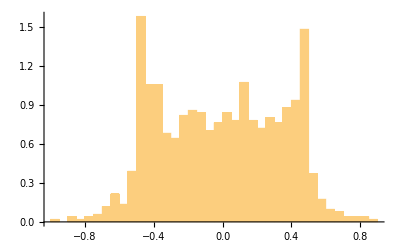

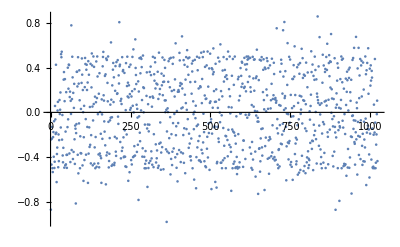

```mathematica
Histogram[Rest@FourierDCT@shiftregistersequence,30,"PDF"]
ListPlot[Rest@FourierDCT@shiftregistersequence]
```

## Conclusion

### Summary

In this project we have successfully implemented 8 unique tests which evaluate both sequences of zeros and ones and sequences of reals between zero and one. The implemented tests are serial, run length, run count, chi square, spectral, Kolmogorov–Smirnov, cumulative sum, and arcsine law tests. Some tests are generated using a Monte Carlo method while others are theoretically derived. Some tests are implemented directly from methods published by NIST. The tests have additionally been applied to test the randomness of rule 30 and linear feedback shift registers; the randomness of rule 30 was not rejected while the randomness of a maximal linear feedback shift register was rejected.

### Future directions

The scope of this project can be extended by implementing more tests–specifically tests that assess the entropy/information within a sequence. Some sequences fail certain tests but not others, so a unified conclusion describing the nature of the non–randomness of a sequence is another possible direction. Including other measures of complexity of a sequence is another possible direction. Randomness, complexity, and information/entropy are all concepts that are deeply intertwined, so creating measures that reflect these concepts could be clarifying. Additionally, computational research into what an ideal α–value might be would be useful. Finally, one could also investigate the applications of randomness testing in more detail to assess systems like non–linear feedback shift registers.

## References

NIST SP 800-22: Random Bit Generation

Lorek, Los, Gotfryd, Zagórski. On testing pseudorandom generators via statistical tests based on the
arcsine law. arXiv:1903.09805.

Knute, Donald E. The Art of Computer Programming. Third Edition, 1938.